```mathematica
f =Prime[n]
```

Prime[n]

```mathematica
Table[Prime[n],{n,1,20}]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71}

```mathematica
EvenQ[f]
```

False

```mathematica
Map[EvenQ,f]
```

{True,False,False,False,False,False,False,False,False,False}

```mathematica
Table[EvenQ[p],{p,f}]
```

{True,False,False,False,False,False,False,False,False,False}

```mathematica
q =Table[PrimePi[n], {n,10}]
```

{0,1,2,2,3,3,4,4,4,4}

```mathematica
w = PrimePi[n]
```

PrimePi[n]

```mathematica
Table[w, {n,20}]
```

{0,1,2,2,3,3,4,4,4,4,5,5,6,6,6,6,7,7,8,8}

```mathematica
Norm[{1,2,3}]
```

√14

```mathematica
Norm[{1,2,3,4,5,6,7,8,9,10}[[1;;3]]]
```

√14

```mathematica
Sqrt[x^2+y^2+z^2]
```

√(x^2+y^2+z^2)

```mathematica
norm[x_,y_,z_]:=√(x^2+y^2+z^2)
```

```mathematica
norm[1,2,3]
```

√14

```mathematica
normList1[v_]:=√(v[[1]]^2+v[[2]]^2+v[[3]]^2)
```

```mathematica
normList1[{1,2,3}]
```

√14

```mathematica
normList2[v_]:=norm@@v
```

```mathematica
normList2[{1,2,3}]
```

√14

```mathematica
normRep[rep_]:=√(x^2+y^2+z^2)/.rep
```

```mathematica
normRep[{x->1,y->2,z->3}]
```

√14

```mathematica
makePlot[data_ , fn_]:=Module[{listPlot,fnPlot,xMin,xMax},xMin =Min[data[[All,1]]]; xMax = Max[data[All,1]]; listPlot =ListPlot[data]; fnPlot = Plot[fn[x],{x,xMin,xMax}];
Show[listPlot,fnPlot]//Return;];
```

Plot::plln: Limiting value {{3, 2}, {4, 2}, {5, 3}, {6, 3}, {7, 4}, {8, 4}, {9, 4}, {10, 4}, {11, 5}, {12, 5}, {13, 6}, {14, 6}, {15, 6}, {16, 6}, {17, 7}, {18, 7}, {19, 8}, {20, 8}, {21, 8}, {22, 8}, {23, 9}, {24, 9}, {25, 9}, {26, 9}, {27, 9}, {28, 9}, {29, 10}, {30, 10}, {31, 11}, {32, 11}, {33, 11}, {34, 11}, {35, 11}, {36, 11}, {37, 12}, {38, 12}, {39, 12}, {40, 12}, {41, 13}, {42, 13}, {43, 14}, {44, 14}, {45, 14}, {46, 14}, {47, 15}, {48, 15}, {49, 15}, {50, 15}, {51, 15}, {52, 15}, « 148 »}[All, 1] in {x, xMin$67304, xMax$67304} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in GraphicsBox[List[List[], List[Hue[0.67`, 0.6`, 0.6`], Directive[RGBColor[0.24720000000000014`, 0.24`, 0.6`]], PointBox[List[List[3.`, 2.`], List[4.`, 2.`], List[5.`, 3.`], List[6.`, 3.`], List[7.`, 4.`], List[8.`, 4.`], List[9.`, 4.`], List[10.`, 4.`], List[11.`, 5.`], List[12.`, 5.`], List[13.`, 6.`], List[14.`, 6.`], List[15.`, 6.`], List[16.`, 6.`], List[17.`, 7.`], List[18.`, 7.`], List[19.`, 8.`], List[20.`, 8.`], List[21.`, 8.`], List[22.`, 8.`], List[23.`, 9.`], List[24.`, 9.`], List[25.`, 9.`], List[26.`, 9.`], List[27.`, 9.`], List[28.`, 9.`], List[29.`, 10.`], List[30.`, 10.`], List[31.`, 11.`], List[32.`, 11.`], List[33.`, 11.`], List[34.`, 11.`], List[35.`, 11.`], List[36.`, 11.`], List[37.`, 12.`], List[38.`, 12.`], List[39.`, 12.`], List[40.`, 12.`], List[41.`, 13.`], List[42.`, 13.`], List[43.`, 14.`], List[44.`, 14.`], List[45.`, 14.`], List[46.`, 14.`], List[47.`, 15.`], List[48.`, 15.`], List[49.`, 15.`], List[50.`, 15.`], List[51.`, 15.`], List[52.`, 15.`], Skeleton[148]]]], List[]], List[Rule[AxesLabel, List[None, None]], Rule[AspectRatio, NCache[Power[GoldenRatio, -1], 0.6180339887498948`]], Rule[Axes, True], Rule[AxesOrigin, List[0, 0]], Rule[Method, List[]], Rule[PlotRange, List[List[0, 200.`], List[0, 46.`]]], Rule[PlotRangeClipping, True], Rule[PlotRangePadding, List[List[4.`, 4.`], List[0.92`, 0.92`]]]]], Plot[(#1/Log[#1] &)[x], {x, xMin$67304, xMax$67304}].

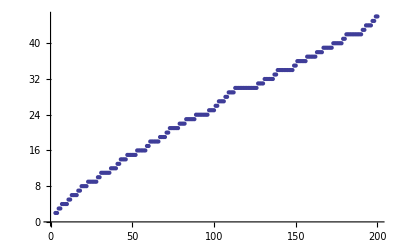
Show[-Graphics-,Plot[(#1/Log[#1]&)[x],{x,xMin$67304,xMax$67304}]]

```mathematica
makePlot[Table[{n,PrimePi[n]},{n,3,200}],#/Log[#]&]
```